## Code

```mathematica
repository = ParentDirectory[NotebookDirectory[]]; 
PacletDirectoryLoad[FileNameJoin[{repository, "Recursor"}]]; 
Needs["WolframInstitute`Recursor`"]
Needs["Wolfram`Lambda`"]
data = Import[FileNameJoin[{repository, "docs", "notes", "data", "OEISMeasurements9110.json.gz"}], {"GZIP", "RawJSON"}]; 
records = data["Sequences"]; 
comparisons = data["Comparisons"]; 

assert[condition_, message_] := If[ !TrueQ[condition], Print["FAILED: ", message]; Abort[]]; 
assert[
	Length[records] === 9110 && 
	Count[Lookup[records, "PrimaryExact"], True] === 897 && 
	Count[Lookup[records, "AllRecordedExact"], True] === 91,
	 "Checkpoint totals"
]; 
assert[AllTrue[records, Take[#1["Matches"], 8] === ConstantArray[1, 8] & ], "Training fits"]; 
assert[
	AllTrue[records, Length[#1["Terms"]] === Length[#1["Matches"]] === Length[#1["Values"]] === Length[#1["Statuses"]] & ], 
	"Complete term records"
]; 

indexed = AssociationThread[Lookup[records, "ID"], records]; 

passed = Select[records, #1["PrimaryExact"] & ]; 

complete = Select[records, #1["AllRecordedExact"] & ];
 
failed = Select[records,  !#1["PrimaryExact"] & ]; 

firstPerfect[record_] := First[FirstPosition[record["FitnessHistory"], 8]] - 1; 
firstFailure[record_] := Replace[FirstPosition[record["Matches"], 0], {position_List :> First[position], _Missing -> Null}]; 
constantPrefixQ[record_] := Length[DeleteDuplicates[Take[record["Terms"], 8]]] === 1; 
constantWLQ[record_] := StringMatchQ[record["WLCode"], RegularExpression["Function\\[n,[0-9]+\\]"]]; 
meanLoss[group_] := N[1 - Mean[Lookup[group, "FitnessHistory"]]/8]; 
weightedLoss[counts_] := N[1 - Range[0, 8] . counts/(8*Total[counts])]; 

primaryLoss = weightedLoss /@ data["PrimaryPassFitnessCounts"]; 

cohortLoss = meanLoss[records]; 

generationCounts = Table[Count[firstPerfect /@ records, generation], {generation, 0, 20}]; 

cohortGroups = GroupBy[records, If[constantPrefixQ[#1], "Constant prefix", "Varying prefix"] & ]; 

lengths = Length /@ Lookup[records, "Terms"];
 
longCohort = Select[records, Length[#1["Terms"]] >= 48 & ]; 

prefixSurvival = Table[{
	horizon, N[100*(Count[(Total[Take[#1["Matches"], 8 + horizon]] == 8 + horizon & ) /@ longCohort, True]/Length[longCohort])]
}, {horizon, 0, 40}]; 

positionAgreement = Table[{position, N[100*Mean[Lookup[longCohort, "Matches"][[All,position]]]]}, {position, 1, 48}]; 

termAgreementCounts = Table[Count[Total /@ (Take[Drop[#1, 8], 12] & ) /@ Lookup[records, "Matches"], score], {score, 0, 12}]; 

primaryStatuses = Counts[Flatten[(Take[Drop[#1, 8], 12] & ) /@ Lookup[records, "Statuses"]]]; 

allStatuses = Counts[Flatten[Lookup[records, "Statuses"]]]; 

primaryOnlyBudgetFailures = Select[failed, AllTrue[Transpose[{Take[Drop[#1["Statuses"], 8], 12], Take[Drop[#1["Matches"], 8], 12]}], First[#1] =!= "Completed" || Last[#1] === 1 & ] & ]; 

arms = {"Evolution", "NoMutation", "NoCrossover", "RandomSearch"}; 

armNames = {"Evolution", "No mutation", "No crossover", "Random search"}; 

armGroups = KeyTake[GroupBy[comparisons, #1["Arm"] & ], arms]; 

assert[And @@ (Length[#1] == 2048 & ) /@ Values[armGroups], "Matched comparison sizes"]; 
assert[SameQ @@ (Sort[Lookup[#1, "ID"]] & ) /@ Values[armGroups], "Matched comparison IDs"]; 

armSummary = KeyValueMap[
	Function[{arm, group}, 
		Association[
			"Arm" -> arm, 
			"Sequences" -> Length[group], 
			"TrainingFits" -> Count[Lookup[group, "TrainingFit"], True], 
			"JointFits" -> Count[Lookup[group, "JointFit"], True], 
			"AllRecordedFits" -> Count[Lookup[group, "AllRecordedFit"], True], 
			"TotalSearchSeconds" -> Total[Lookup[group, "ActualSearchSeconds"]], 
			"MedianLogicalTrialSeconds" -> Median[Lookup[group, "SearchSeconds"]]
		]
	], armGroups
]; 

armCurves = (N[1 - Mean[Lookup[#1, "History"]]/8] & ) /@ armGroups; 

armIndex = AssociationMap[AssociationThread[Lookup[armGroups[#1], "ID"], armGroups[#1]] & , arms]; 

pairContrasts = AssociationMap[
	Function[arm, 
		With[{pairs = Transpose[{Values[KeySort[armIndex["Evolution"]]], Values[KeySort[armIndex[arm]]]}]}, 
			Association[
				"EvolutionOnly" -> Count[(#1[[1]]["JointFit"] &&  !#1[[2]]["JointFit"] & ) /@ pairs, True], 
				"ComparisonOnly" -> Count[( !#1[[1]]["JointFit"] && #1[[2]]["JointFit"] & ) /@ pairs, True]
			]
		]
	], Rest[arms]
]; 

deepGroups = Association[
	"Standard" -> Select[armGroups["Evolution"], #1["DeepCohort"] & ], 
	"Larger and deeper" -> Select[comparisons, #1["Arm"] === "DeepEvolution" & ]
]; 

assert[And @@ (Length[#1] == 1024 & ) /@ Values[deepGroups], "Deep comparison sizes"]; 

deepCurves = (N[1 - Mean[Lookup[#1, "History"]]/8] & ) /@ deepGroups; 

deepSummary = KeyValueMap[
	Function[{arm, group}, 
		Association[
			"Arm" -> arm, 
			"Sequences" -> Length[group], 
			"TrainingFits" -> Count[Lookup[group, "TrainingFit"], True], 
			"JointFits" -> Count[Lookup[group, "JointFit"], True], 
			"AllRecordedFits" -> Count[Lookup[group, "AllRecordedFit"], True], 
			"TotalSearchSeconds" -> Total[Lookup[group, "ActualSearchSeconds"]]
		]
	], deepGroups
]; 

baselineOverlap = Association[
	"Both" -> Length[Select[records, #1["PrimaryExact"] && #1["AffineBaselinePrimaryExact"] & ]], 
	"RecursorOnly" -> Length[Select[records, #1["PrimaryExact"] &&  !#1["AffineBaselinePrimaryExact"] & ]]
]; 

baselineOverlap["AffineOnly"] = data["Baselines"]["AffineJointFits"] - baselineOverlap["Both"]; 

baselineOverlap["RecursorOnlyAllRecorded"] = Length[Select[complete,  !#1["AffineBaselinePrimaryExact"] & ]]; 

groupSummary = KeyValueMap[
	Function[{name, group}, 
		Association[
			"Group" -> name, 
			"TrainingFits" -> Length[group], 
			"JointFits" -> Count[Lookup[group, "PrimaryExact"], True], 
			"AllRecordedFits" -> Count[Lookup[group, "AllRecordedExact"], True]
		]
	], cohortGroups
]; 

exampleIDs = {"A028552", "A037915", "A191967", "A000030", "A002837", "A006983"}; 

assert[And @@ (KeyExistsQ[indexed, #1] & ) /@ exampleIDs, "Illustration IDs"]; 

numeric[value_String] /; StringMatchQ[value, DigitCharacter..] := FromDigits[value]; 

numeric[_] := Missing["Unfinished"]; 

predictionPlot[id_, count_:All] := Module[{record = indexed[id], amount, inputs, observed, predicted}, 
	amount = If[count === All, Length[record["Terms"]], Min[count, Length[record["Terms"]]]]; 
	inputs = Range[record["Offset"], record["Offset"] + amount - 1]; 
	observed = Take[record["Terms"], amount]; 
	predicted = numeric /@ Take[record["Values"], amount]; 
	ListPlot[{Transpose[{inputs, observed}], Transpose[{inputs, predicted}]}, 
		Joined -> {True, False}, 
		PlotMarkers -> Automatic, 
		PlotLegends -> {"OEIS", "Recursor"}, 
		Frame -> True, 
		FrameLabel -> {"Original index n", "a(n)"}, 
		PlotLabel -> id, 
		GridLines -> {{record["Offset"] + 7.5, record["Offset"] + 19.5}, None}, 
		PlotRange -> All
	]
]
 
firstFitGenerations = (First[FirstPosition[#1["FitnessHistory"], 8]] - 1 & ) /@ records; 

individualLoss = (1 - #1["FitnessHistory"]/8 & ) /@ Lookup[indexed, {"A028552", "A037915", "A191967", "A002837"}]; 

prefixSizes = ReverseSort[Values[Counts[Lookup[records, "TrainingKey"]]]]; 

illustrationIDs = {"A028552", "A037915", "A191967", "A002837"}; 

heatRecords = Take[SortBy[longCohort, Hash[StringJoin["Recursor-report-9110:", #1["ID"]], "SHA256"] & ], 128]; 

heatValues = Transpose[(Take[#1, 48] & ) /@ Lookup[heatRecords, "Matches"]]; 

parent = Rec[Var, Const[1], Mul[Succ[Idx], Acc]]; 

mutationExample = Association[
	"Seed" -> 2, 
	"Site" -> BlockRandom[SeedRandom[2]; RandomChoice[RecursorSites[parent]]], 
	"Mutant" -> BlockRandom[SeedRandom[2]; MutateRecursor[parent, 3]]
]; 

assert[FormatRecursor[mutationExample["Mutant"]] === "Rec[Var, Const[1], Mul[Succ[Acc], Acc]]", "Mutation illustration"];
```

## Init

```mathematica
metrics = Association[
"CutoffUTC"->data["CutoffUTC"],
"Eligible"->data["Protocol"]["EligibleCount"],
"TotalRecords"->data["Protocol"]["SequenceCount"],
"CoveredWithValidatedProgram"->data["HistoricalSelectedCount"],
"TrainingFits"->Length[records],
"PrimaryFits"->Length[passed],
"AllRecordedFits"->Length[complete],
"ConditionalPrimaryPercent"->N[100*(Length[passed]/Length[records])], 
"ConditionalAllRecordedPercent"->N[100*(Length[complete]/Length[records])], 
"CorpusPrimaryPercent"->N[100*(Length[passed]/data["Protocol"]["EligibleCount"])], 
"CorpusAllRecordedPercent"->N[100*(Length[complete]/data["Protocol"]["EligibleCount"])], 
"FirstPass"->data["PrimaryPass"],
"FirstPassStatuses"->data["PrimaryPassStatuses"], 
"DistinctTrainingPrefixes"->Length[DeleteDuplicates[Lookup[records,"TrainingKey"]]], 
"DistinctPrimaryFitPrefixes"->Length[DeleteDuplicates[Lookup[passed,"TrainingKey"]]], 
"DistinctAllRecordedFitPrefixes"->Length[DeleteDuplicates[Lookup[complete,"TrainingKey"]]], 
"DistinctPrograms"->Length[DeleteDuplicates[Lookup[records,"Program"]]], 
"DistinctAllRecordedPrograms"->Length[DeleteDuplicates[Lookup[complete,"Program"]]], 
"ConstantWLPrimaryFits"->Length[Select[passed,constantWLQ]], 
"ConstantWLAllRecordedFits"->Length[Select[complete,constantWLQ]],
"InitialTrainingFits"->First[generationCounts],
"FirstPerfectGenerationCounts"->generationCounts,
"MedianFirstPerfectGeneration"->Median[firstPerfect /@ records],
"PrimaryMeanInitialLoss"->First[primaryLoss],
"PrimaryMeanFinalLoss"->Last[primaryLoss],
"SelectedMeanInitialLoss"->First[cohortLoss],
"SelectedMeanFinalLoss"->Last[cohortLoss],
"LongCohortSize"->Length[longCohort],
"RecordedTermsMinimum"->Min[lengths],
"RecordedTermsMedian"->Median[lengths],
"RecordedTermsMaximum"->Max[lengths],
"PrimaryEvaluationStatuses"->primaryStatuses,
"AllEvaluationStatuses"->allStatuses,
"PrimaryFailuresWithoutObservedWrongValue"->Length[primaryOnlyBudgetFailures], 
"WLVerificationStatuses"->Counts[Lookup[records,"WLStatus"]], 
"TrainingFitnessRecheckFailures"->Count[Lookup[records,"TrainingFitnessRechecked"],False], 
"Baselines"->data["Baselines"],
"BaselineOverlap"->baselineOverlap,
"PrefixGroups"->groupSummary,
"Arms"->armSummary,
"PairedContrasts"->pairContrasts,
"DeepArms"->deepSummary, 
"Examples" -> (Join[KeyTake[#1,{"ID","Name","Offset","Program","Nodes","Seed","WLCode","WLStatus","PrimaryExact", "AllRecordedExact"}],Association["RecordedTerms"->Length[#1["Terms"]], "FirstPerfectGeneration"->firstPerfect[#1],"FirstFailurePosition"->firstFailure[#1]]]& )/@Lookup[indexed, exampleIDs], 
"SourceDataSHA256" -> IntegerString[FileHash[FileNameJoin[{repository,"docs","notes","data","OEISMeasurements9110.json.gz"}],"SHA256"],16,64],"WolframVersion"->$Version,"SystemID"->$SystemID
];
```

## Results

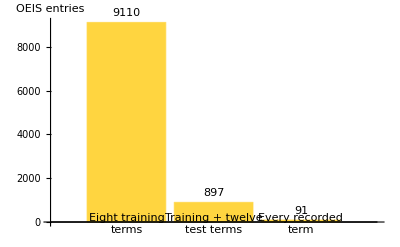

```mathematica
BarChart[
Lookup[metrics,{"TrainingFits","PrimaryFits","AllRecordedFits"}],
ChartLabels->{"Eight training\nterms","Training + twelve\ntest terms","Every recorded\nterm"},
LabelingFunction -> Above, AxesLabel -> {None, "OEIS entries"}
]
```

Figure 1. Of 9,110 programs that match the first eight terms, 897 match the next twelve and 91 match every stored term.

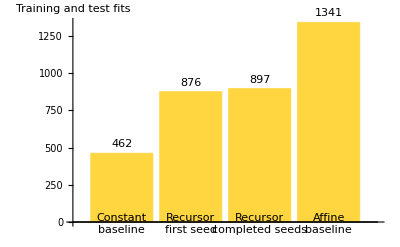

```mathematica
BarChart[{
data["Baselines"]["ConstantJointFits"],
data["PrimaryPass"]["JointFits"],
metrics["PrimaryFits"],
data["Baselines"]["AffineJointFits"]
}, 
ChartLabels->{"Constant\nbaseline","Recursor\nfirst seed","Recursor\ncompleted seeds","Affine\nbaseline"}, 
LabelingFunction->Above,
AxesLabel->{None,"Training and test fits"}
]
```

Figure 2. Of 283,167 eligible sequences, Recursor matches the first twenty terms for 897; a straight-line formula matches 1,341.

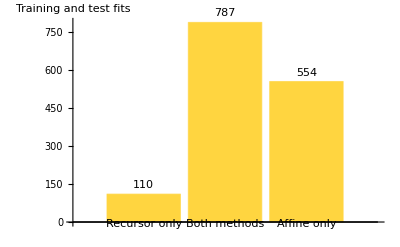

```mathematica
BarChart[
Lookup[metrics["BaselineOverlap"],{"RecursorOnly","Both","AffineOnly"}], 
ChartLabels->{"Recursor only","Both methods","Affine only"},
LabelingFunction->Above,
AxesLabel->{None,"Training and test fits"}
]
```

Figure 3. Recursor matches 110 sequences missed by the straight-line baseline, but matches fewer sequences overall.

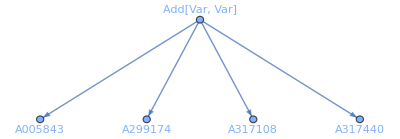

```mathematica
Graph[
(DirectedEdge["Add[Var, Var]", #1] & )/@Lookup[Select[complete,#1["Program"]==="Add[Var, Var]"&],"ID"], 
VertexLabels->"Name",
GraphLayout->{"LayeredEmbedding","RootVertex"->"Add[Var, Var]"}
]
```

Figure 4. One program, 2n, matches every stored term of four different OEIS entries.

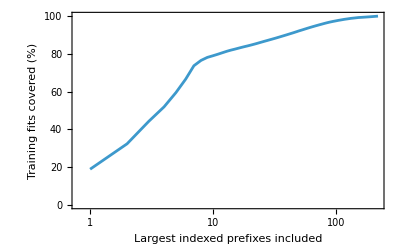

```mathematica
ListLogLinearPlot[
Transpose[{Range[Length[prefixSizes]],100*(Accumulate[prefixSizes]/Total[prefixSizes])}],
Joined->True,
Frame->True,
FrameLabel->{"Largest indexed prefixes included","Training fits covered (%)"},
PlotRange->{0,100}
]
```

Figure 5. The 9,110 fits contain only 221 different combinations of starting index and first eight terms.

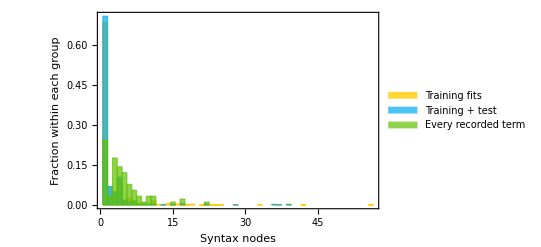

```mathematica
Histogram[
(Lookup[#1, "Nodes"] & )/@{records,passed,complete},
{0.5,Max[Lookup[records,"Nodes"]]+0.5,1},
"Probability",
ChartLegends->{"Training fits","Training + test","Every recorded term"},
Frame->True,
FrameLabel->{"Syntax nodes","Fraction within each group"}
]
```

Figure 6. Program sizes for training fits, programs matching the next twelve terms, and programs matching every stored term.

## Programs that match every recorded term

```mathematica
polynomialprogram=Mul[Add[Succ[Var],Const[2]],Var];
```

```mathematica
roundarithmeticprogram=Monus[Succ[Pred[Var]],Half[Half[Pred[Var]]]];
```

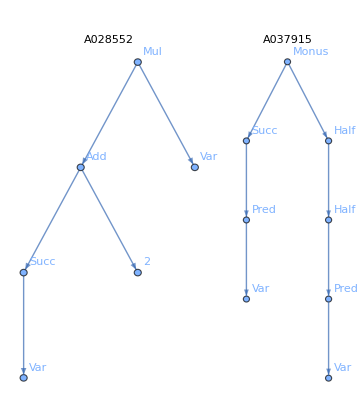

```mathematica
GraphicsGrid[{{
RecursorProgramTree[polynomialprogram, PlotLabel -> "A028552"], 
RecursorProgramTree[roundarithmeticprogram, PlotLabel -> "A037915"]
}},ImageSize->Medium]
```

Figure 7. Program trees for A028552, n (n + 3), and A037915, Quotient[3 n + 4, 4].

#### n (n + 3)

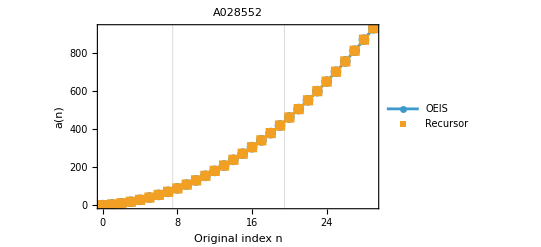

```mathematica
predictionPlot["A028552", 30]
```

Figure 8. A028552: n (n + 3) matches all 51 stored terms; the first 30 are shown.

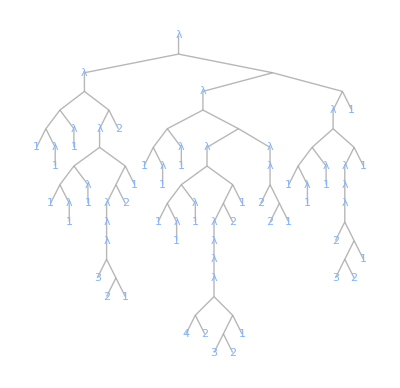

```mathematica
LambdaTree[CompileRecursor[polynomialprogram]]
```

Figure 9. Compiled lambda tree for A028552: n (n + 3).

#### Quotient[3 n + 4, 4]

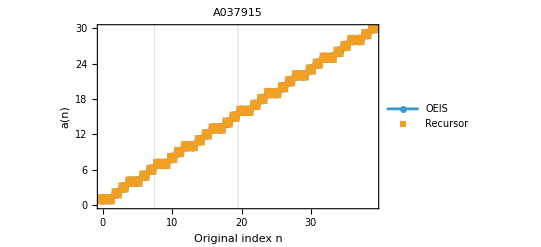

```mathematica
predictionPlot["A037915", 40]
```

Figure 10. A037915: Quotient[3 n + 4, 4] matches all 73 stored terms; the first 40 are shown.

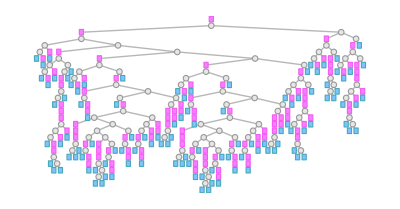

```mathematica
LambdaTree[CompileRecursor[roundarithmeticprogram],PlotTheme->"Minimal"]
```

Figure 11. Compiled lambda tree for A037915: Quotient[3 n + 4, 4].

#### n^2

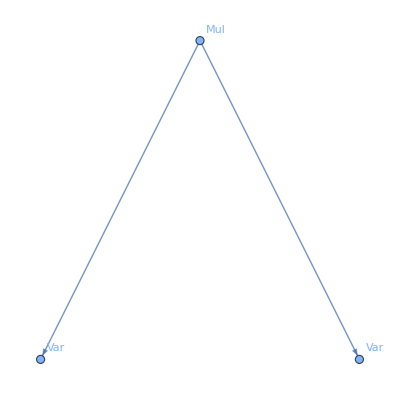
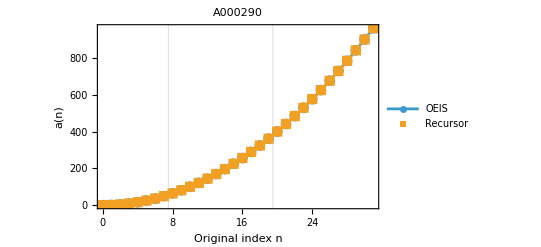
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[Mul[Var,Var]],predictionPlot["A000290",32]}}]
```

Figure 12. A000290: squares, n^2. All 51 stored terms match; the first 32 are shown.

```mathematica
LambdaTree[CompileRecursor[Mul[Var,Var]]]
```

-Graphics-

Figure 13. Compiled lambda tree for A000290: n^2.

#### n^3

```mathematica
cubicprogram=Mul[Mul[Var,Var],Mul[Var,Const[3]]];
```

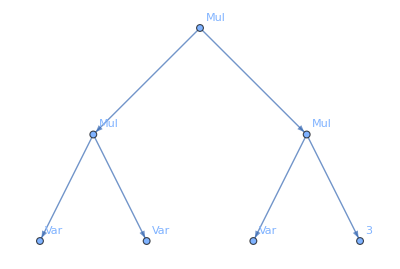
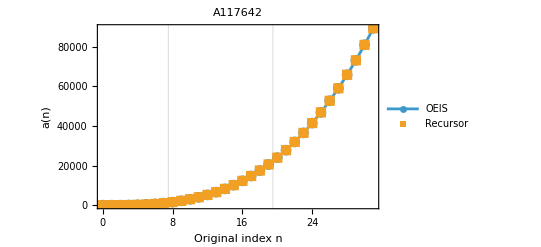
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[cubicprogram],predictionPlot["A117642",32]}}]
```

Figure 14. A117642: 3 n^3. All 40 stored terms match; the first 32 are shown.

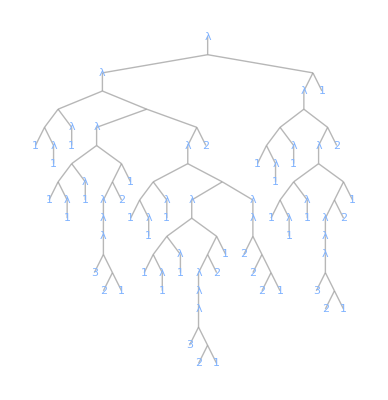

```mathematica
LambdaTree[CompileRecursor[cubicprogram]]
```

Figure 15. Compiled lambda tree for A117642: 3 n^3.

#### n Quotient[n, 2] ^ 2

```mathematica
roundedproductprogram=Mul[Mul[Var,Half[Var]],Half[Var]];
```

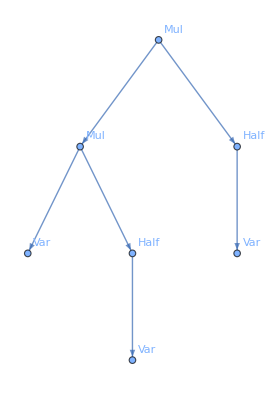
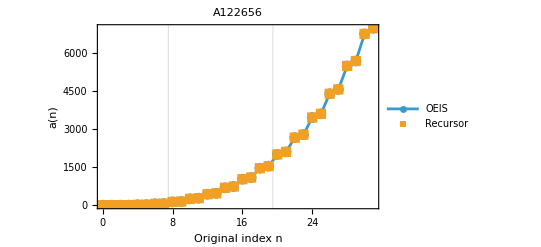
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[roundedproductprogram],predictionPlot["A122656",32]}}]
```

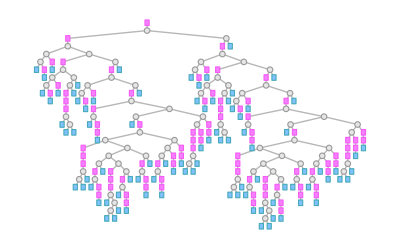

```mathematica
LambdaTree[CompileRecursor[roundedproductprogram],PlotTheme->"Minimal"]
```

Figure 17. Compiled lambda tree for A122656: n Quotient[n, 2]^2.

#### n + Quotient[Max[0, n - 1], 2]

```mathematica
skipmultiplesprogram=Add[Half[Pred[Var]],Var];
```

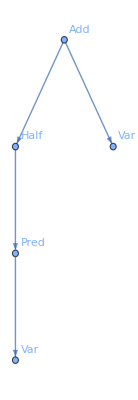
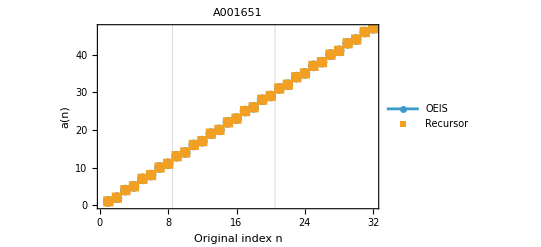
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[skipmultiplesprogram], predictionPlot["A001651", 32]}}]
```

Figure 18. A001651: positive integers that are not multiples of three. All 70 stored terms match.

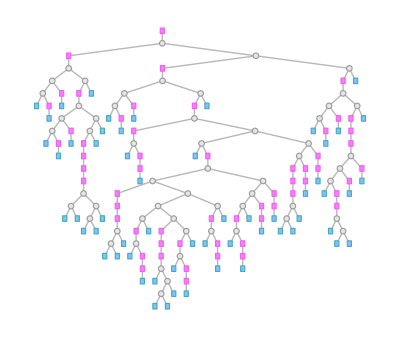

```mathematica
LambdaTree[CompileRecursor[skipmultiplesprogram],PlotTheme->"Minimal"]
```

Figure 19. Compiled lambda tree for A001651: n + Quotient[Max[0, n - 1], 2].

#### Mod[Quotient[n, 2], 3]

```mathematica
periodicprogram=Rem[Half[Var],Const[3]];
```

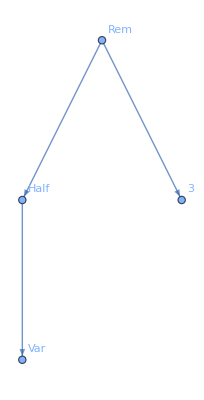
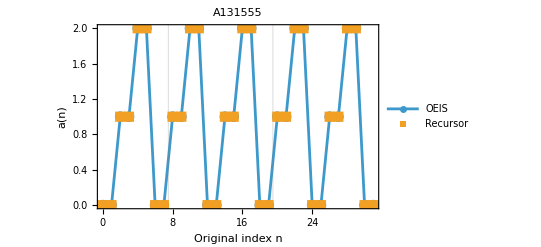
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[periodicprogram],predictionPlot["A131555",32]}}]
```

Figure 20. A131555: the block 0, 0, 1, 1, 2, 2 repeats. All 105 stored terms match.

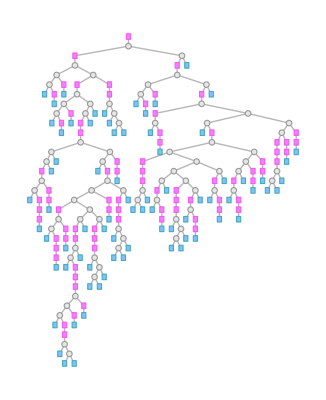

```mathematica
LambdaTree[CompileRecursor[periodicprogram],PlotTheme->"Minimal"]
```

Figure 21. Compiled lambda tree for A131555: Mod[Quotient[n, 2], 3].

#### Mod[n, 3]

```mathematica
residueprogram=CoRec[Const[3],Rem[Var,Idx]];
```

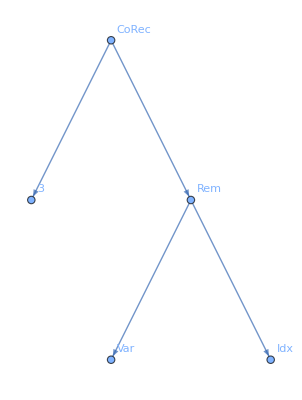
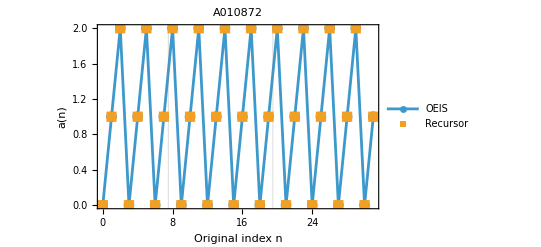
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[residueprogram],predictionPlot["A010872",32]}}]
```

Figure 22. A010872: remainders after division by three. All 105 stored terms match.

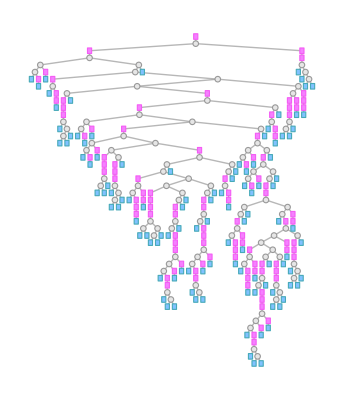

```mathematica
LambdaTree[CompileRecursor[residueprogram],PlotTheme->"Minimal"]
```

Figure 23. Compiled lambda tree for A010872: Mod[n, 3].

#### If[n < 2, 0, n + 1]

```mathematica
conditionalprogram=Ifz[Pred[Var],Const[0],Succ[Var]];
```

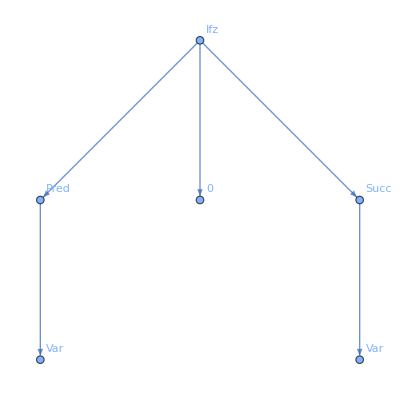
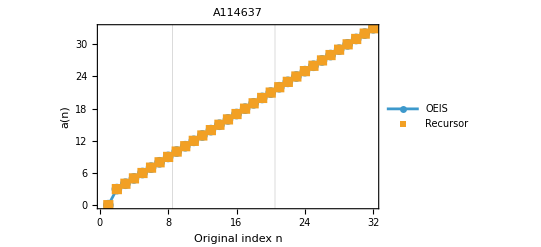
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[conditionalprogram],predictionPlot["A114637",32]}}]
```

Figure 24. A114637: 0, 3, 4, 5, .... All 73 stored terms match.

```mathematica
LambdaTree[CompileRecursor[conditionalprogram]]
```

-Graphics-

Figure 25. Compiled lambda tree for A114637: If[n < 2, 0, n + 1].

#### n + Quotient[Max[0, n - 1], 2] + Quotient[Max[0, n - 1], 4]

```mathematica
residueclassprogram=Add[Half[Pred[Var]],Add[Half[Half[Pred[Var]]],Var]];
```

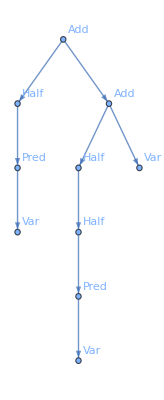
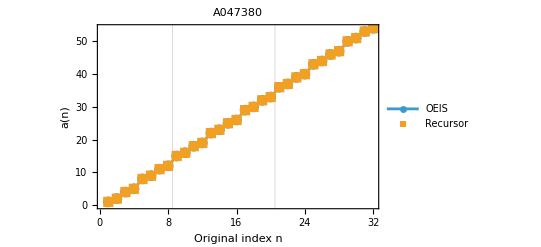
-Graphics- | -Graphics-

```mathematica
Grid[{{RecursorProgramTree[residueclassprogram],predictionPlot["A047380",32]}}]
```

Figure 26. A047380: positive integers with remainder 1, 2, 4 or 5 on division by seven. All 64 stored terms match.

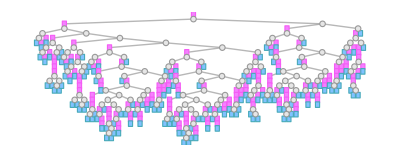

```mathematica
LambdaTree[CompileRecursor[residueclassprogram],PlotTheme->"Minimal"]
```

Figure 27. Compiled lambda tree for A047380: n + Quotient[Max[0, n - 1], 2] + Quotient[Max[0, n - 1], 4].

## Mutation function

```mathematica
parent=Rec[Var,Const[1],Mul[Succ[Idx],Acc]];
```

```mathematica
mutant=BlockRandom[SeedRandom[2];MutateRecursor[parent,3]];
```

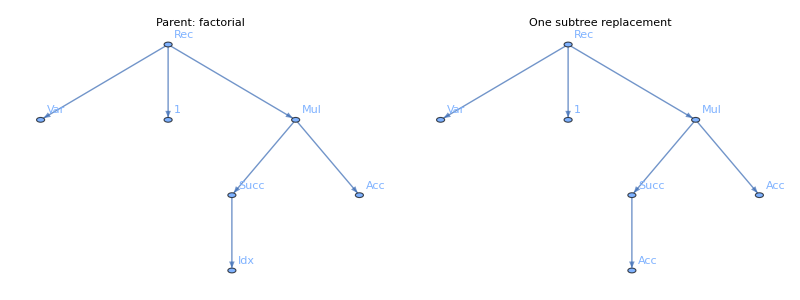

```mathematica
Grid[{{RecursorProgramTree[parent, PlotLabel -> "Parent: factorial"], RecursorProgramTree[mutant, PlotLabel -> "One subtree replacement"]}}]
```

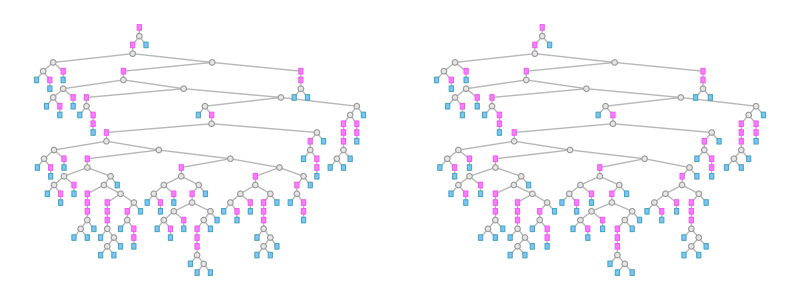

```mathematica
Grid[{{LambdaTree[CompileRecursor[parent],PlotTheme->"Minimal"],LambdaTree[CompileRecursor[mutant],PlotTheme->"Minimal"]}}]
```

Figure 28. Replacing Idx with Acc changes factorial into a(0) = 1, a(n+1) = a(n) (a(n)+1); this is a separate example.

## Loss curves

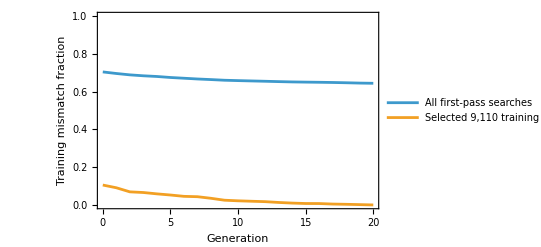

```mathematica
ListLinePlot[
{primaryLoss,cohortLoss},
DataRange->{0, 20},
PlotLegends->{"All first-pass searches","Selected 9,110 training fits"},
Frame->True,
FrameLabel->{"Generation","Training mismatch fraction"},
PlotRange->{0,1}
]
```

Figure 29. Average training loss for all first searches (blue) and only the successful training fits (orange).

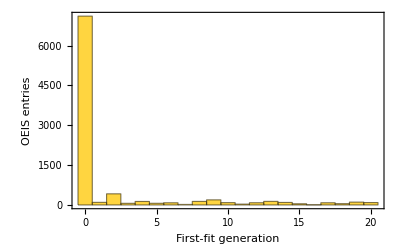

```mathematica
Histogram[firstFitGenerations,{-0.5,20.5,1},
Frame->True,
FrameLabel->{"First-fit generation", "OEIS entries"}
]
```

Figure 30. 7,107 of the 9,110 selected runs already match all eight training terms before evolution starts.

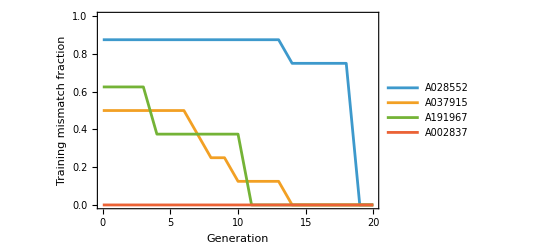

```mathematica
ListLinePlot[
individualLoss,
DataRange->{0,20},
PlotLegends->illustrationIDs,
Frame->True,
FrameLabel->{"Generation","Training mismatch fraction"},
PlotRange->{0,1}
]
```

## Generalization

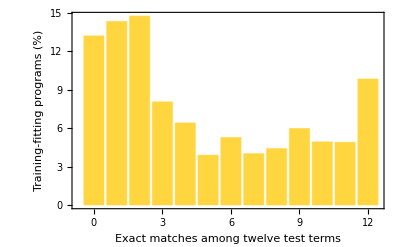

```mathematica
BarChart[
100*(termAgreementCounts/Length[records]),
ChartLabels->Range[0,12],
Frame->True,
FrameLabel->{"Exact matches among twelve test terms", "Training-fitting programs (%)"}
]
```

Figure 32. How many of the next twelve terms each program gets right; 897 programs get all twelve right.

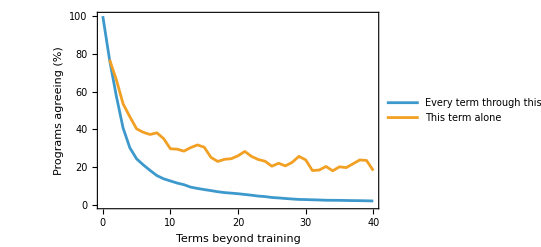

```mathematica
ListLinePlot[
{prefixSurvival,Drop[positionAgreement, 8]/.{position_Integer,value_Real}:>{position-8,value}}, 
PlotLegends->{"Every term through this position","This term alone"},
Frame->True,
FrameLabel->{"Terms beyond training","Programs agreeing (%)"},
PlotRange->{0,100}
]
```

Figure 33. The same 7,840 programs predict farther into their sequences; the blue line requires every preceding prediction to match.

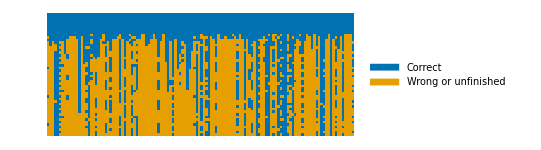

```mathematica
ArrayPlot[1-heatValues,
ColorRules->{0->RGBColor["#0072B2"],1->RGBColor["#E69F00"]}, 
PlotLegends->SwatchLegend[{"Correct","Wrong or unfinished"}], 
FrameTicks->{{Table[{i,i},{i,{1,8,20,32,48}}],None},{Table[{i,i},{i,{1,32,64,96,128}}],None}}, 
FrameLabel->{"Recorded term position","Program in a fixed sample"}
]
```

Figure 34. Each column is a program: blue marks correct predictions,orange marks wrong or unfinished predictions.

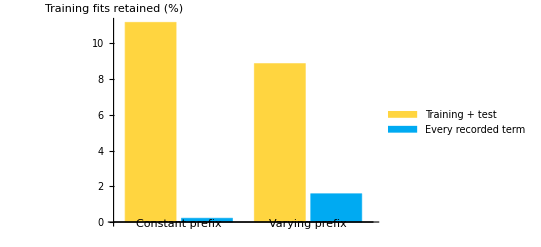

```mathematica
BarChart[
({100*(#1["JointFits"]/#1["TrainingFits"]),100*(#1["AllRecordedFits"]/#1["TrainingFits"])}& )/@groupSummary, 
ChartLabels->{Lookup[groupSummary, "Group"], None},
ChartLegends->{"Training + test","Every recorded term"},
AxesLabel->{None,"Training fits retained (%)"}
]
```

179 of 109,320 primary-test evaluations hit the step budget. 
Ten candidate programs fail this test solely through unfinished evaluations, without an observed wrong value; 
budget exhaustion does not prove non-termination.

Figure 35. How often programs trained on constant or changing terms also match later terms.

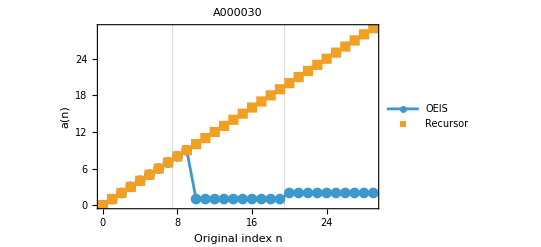

```mathematica
predictionPlot["A000030",30]
```

Figure 36. A000030: n matches the first ten terms, then predicts 10 where the next value is 1.

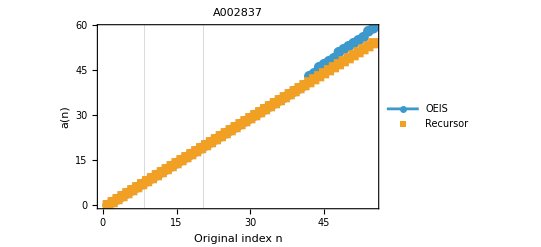

```mathematica
predictionPlot["A002837",55]
```

Figure 37. A002837: n - 1 matches 41 terms, then predicts 41 where the next value is 43.

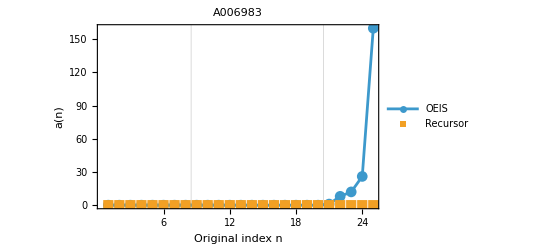

```mathematica
predictionPlot["A006983", 25]
```

Figure 38. A006983 begins with twenty zeros, but its next term is 1; a constant-zero program fails there.

## Does mutation or a larger search help?

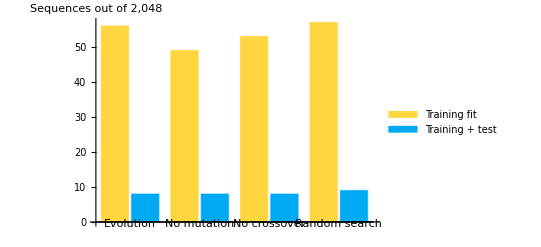

```mathematica
BarChart[
Lookup[armSummary,{"TrainingFits", "JointFits"}],
ChartLabels->{armNames,None},
ChartLegends->{"Training fit","Training + test"},
AxesLabel->{None,"Sequences out of 2,048"}
]
```

Figure 39. Evolution matches all twenty terms for eight of 2,048 sequences; 
without mutation it still matches eight, and random search matches nine.

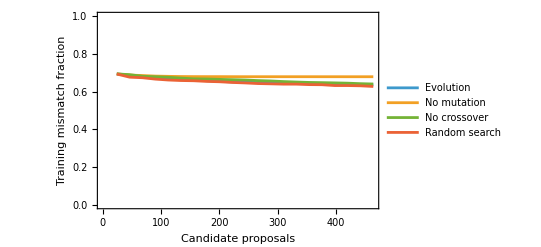

```mathematica
ListLinePlot[
Values[armCurves],
DataRange->{24,464},
PlotLegends->armNames,
Frame->True,
FrameLabel->{"Candidate proposals","Training mismatch fraction"},
PlotRange->{0,1}
]
```

Figure 40. Training loss across methods given 464 candidate programs each.

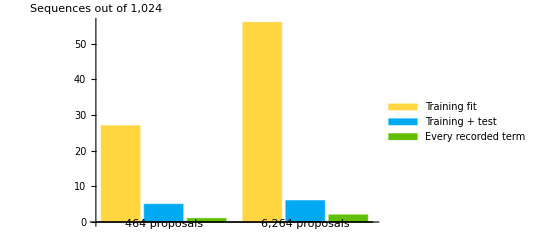

```mathematica
BarChart[
Lookup[deepSummary,{"TrainingFits","JointFits","AllRecordedFits"}], 
ChartLabels->{{"464 proposals","6,264 proposals"},None}, 
ChartLegends->{"Training fit","Training + test","Every recorded term"}, 
AxesLabel->{None,"Sequences out of 1,024"}
]
```

Figure 41. A larger search improves the fit to the first eight terms much more than its predictions of the next twelve.

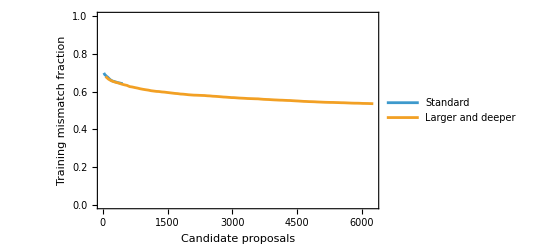

```mathematica
ListLinePlot[{
Transpose[{Range[24,464,22],deepCurves["Standard"]}],
Transpose[{Range[64,6264,62],deepCurves["Larger and deeper"]}]
},
PlotLegends->Keys[deepCurves],
Frame->True,
FrameLabel->{"Candidate proposals","Training mismatch fraction"},
PlotRange->{0,1}
]
```

Figure 42. Extra search lowers training loss, but does not by itself show better predictions.